```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10;
x = Cos[π/4];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"][[2]]
```

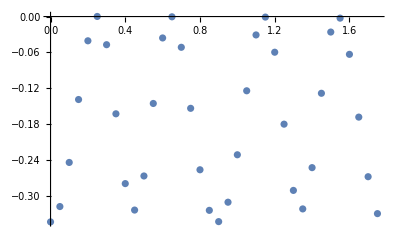

```mathematica
l=3;
m=1;
k=2;

ω = m Ωϕ + k Ωθ;

If[]
ListPlot[Table[{λ,SpinWeightedSpheroidalHarmonicS[0,l,m,a ω,θ[λ],0]Cos[ω t[λ]-m ϕ[λ]]},{λ,0,(2π)/Υ,.05}]]
```

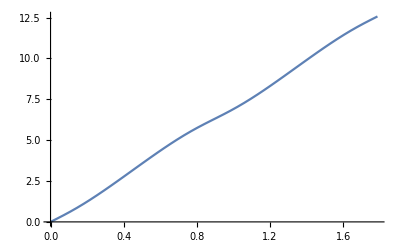

```mathematica
Plot[ω t[λ]-m ϕ[λ],{λ,0,(2π)/Υ}]
```